# ■ Analisis MAV 2

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{NotebookDirectory[],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","DAX","IPC","Nikkei 225"};
```

```mathematica
DaysInYear[year_] := First[DateDifference[{year, 1, 1}, {year, 12, 31}]] + 1;

YearPercentual[date_] := N[QuantityMagnitude[DateDifference[DateObject[{date["Year"], 1, 1}], date]] / DaysInYear[date["Year"]]] + date["Year"];

DateFromYearPercentual[yearPercentual_] := Block[{year, daysEllapsed, date},
	year = IntegerPart[yearPercentual];
	daysEllapsed = IntegerPart[(yearPercentual - year) * DaysInYear[year]];
	date = DatePlus[DateObject[{year, 1, 1}], daysEllapsed];
	Return[date];
];
```

## Obtendremos los datos del mercado 1, para una ventana de 50 dias.

La siguiente linea devuelve fechas percentuales y precios

```mathematica
percentuales=MapAt[YearPercentual, database[[1]]["DatedPrices"], {All,1}];
```

```mathematica
(*lo anterior tiene un Length 6466*)
```

La siguiente linea devuelve un formato de fecha del percentual al formato de fecha de mathematica.

```mathematica
fechas=Map[DateFromYearPercentual[#]&,percentuales[[All,1]]];
```

Ahora se asigna cada fecha su respectivo retorno de precio

```mathematica
precios=database[[1]]["Returns"];
```

Como los retornos se comen un dato, usamos drop para descartar la primera fecha

```mathematica
dateMenos1=Drop[fechas,-1];
```

Asociar a cada fecha su retorno

```mathematica
datereturn=Transpose[{dateMenos1,precios}];
```

Un paréntesis importante. Se calcula μ y σ de los retornos tal cual se tienen. Esto será de utilidad más adelante para simular los retornos.

De los retornos simulados se obtiene μ y σ.

```mathematica
μ= Mean[datereturn[[All,2]]];
σ=StandardDeviation[datereturn[[All,2]]];
```

### Cerrando ese parentesis, se continua con los retornos del mercado 1.

Se estandarizan los retornos.

```mathematica
retuREstandarizado=Standardize[datereturn[[All,2]]];
```

Ya estandarizado, se calcula la media movil para los retornos de los datos reales.

```mathematica
MAVr=MovingAverage[datereturn[[All,2]],50];
```

```mathematica
Length[datereturn[[All,2]]]-Length[MovingAverage[datereturn[[All,2]],50]]
```

49

```mathematica
dateMenosDias=Drop[datereturn[[All,1]],-49];
```

Se obtiene fecha y valor del retorno YA CON MAV de 50 dias

```mathematica
MAVretDate=Transpose[{dateMenosDias,MAVr}];
```

## Ahora si, simulamos un mercado y calculamos su MAV

```mathematica
SimulatedReturns=RandomVariate[NormalDistribution[μ,σ],Length[precios]];
```

Estandarizar los retornos simulados

```mathematica
returnSimuEstandarizado=Standardize[SimulatedReturns];
```

Ya estandarizados, se calcula la media movil para los retornos simulados

```mathematica
MAVs=MovingAverage[returnSimuEstandarizado,50];
```

```mathematica
MAVretDateSimul=Transpose[{dateMenosDias,MAVs}];
```

## Ya aplicada la MAV a reales y simulados se realiza el proceso de discretizacion a partir de haber filtrado los datos con la ventana de 50 días

```mathematica
QMAVr=Quantile[MAVr,{1/4,1/2,3/4}];
QMAVs=Quantile[MAVs,{1/4,1/2,3/4}];
```

Se definen los intervalos de -∞ a ∞ y posteriormente se hace una función que facilite y designe automaticamente los intervalos

```mathematica
intMAVr=Partition[Join[{-∞},QMAVr,{∞}],2,1];
intMAVs=Partition[Join[{-∞},QMAVs,{∞}],2,1];
reglas[intervalo_]:=MapThread[(x_/;IntervalMemberQ[Interval[#1],x])->#2&,{intervalo,Range[4]}];
```

Ahora se aplica reglas a intMAVr y  a intMAVs

```mathematica
rulesToMAVr=reglas[intMAVr];
rulesToMAVs=reglas[intMAVs];
```

Con la siguiente linea se etiquetan los retornos discretos tras ser filtrados por un MAV

```mathematica
DiscretReturnMAVr=MAVr/.rulesToMAVr;
DiscretReturnMAVs=MAVs/.rulesToMAVs;
```

#### no olvidar {fecha,retorno}

Esto nos devuelve fecha y retorno discretizado

```mathematica
dateDiscRetunMAVr=Transpose[{dateMenosDias,DiscretReturnMAVr}];
dateDiscReturnMAVs=Transpose[{dateMenosDias,DiscretReturnMAVs}];
```

## Se procede a calcular entropias

Recordar que en este punto, la media movil ya se trabajo, y esta ventana de tiempo no tiene nada que ver con MAV, es un calculo meramente de la entropia.

Entropia para retornos reales

```mathematica
partReturnMAVr[dias_]:=Partition[dateDiscRetunMAVr,dias,1];
```

```mathematica
SMAVr=Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,particionRetReal[60]];
```

#### Entropia para retornos simulados

```mathematica
partReturnMAVs[dias_]:=Partition[dateDiscReturnMAVs,dias,1];
```

```mathematica
SMAVs=Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,partReturnMAVs[60]];
```

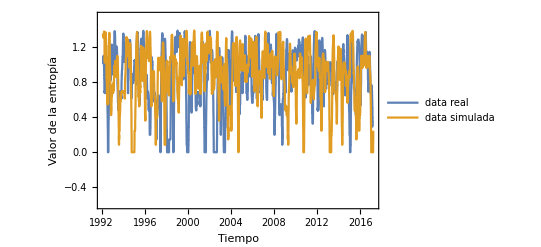

```mathematica
DateListPlot[{SMAVr,SMAVs},PlotRange->{-0.6,1.55},Frame->True,FrameLabel->{{"Valor de la entropía","2017"},{"Tiempo","Entropía de retornos reales y simulados"}},PlotLegends->{"data real", "data simulada"}]
```

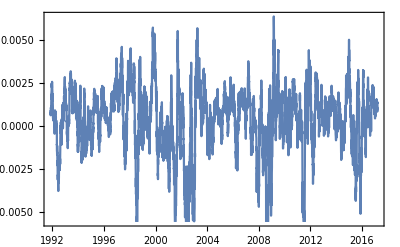

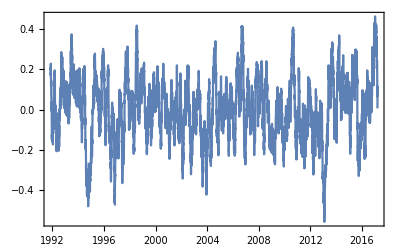

```mathematica
DateListPlot[MAVretDate]
DateListPlot[MAVretDateSimul]
```